α' = 3484.8 meV nm^2/V

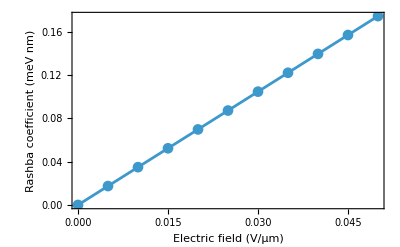

Calculating spin–orbit length:

Electric field (V/µm) | Spin–orbit length (μm)
0.00500000000000000097 | 65.0775
0.0100000000000000019 | 32.5388
0.0150000000000000029 | 21.6925
0.0200000000000000039 | 16.2694
0.0250000000000000049 | 13.0155
0.0300000000000000058 | 10.8463
0.0350000000000000033 | 9.29679
0.0400000000000000078 | 8.13469
0.0450000000000000122 | 7.23084
0.0500000000000000028 | 6.50775

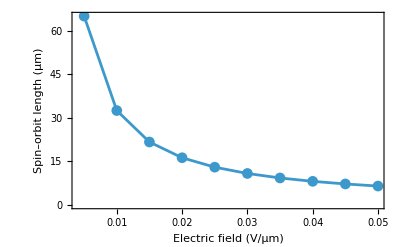

```mathematica
SetDirectory[NotebookDirectory[]];

(* Import data, excluding the header *)
rashbay = Import["Pymablock_Y_kx0.001_emax_0.05_N100_L300.dat"][[2 ;;]];
rashbaz = Import["Pymablock_Z_kx0.001_emax_0.05_N100_L300.dat"][[2 ;;]];


Ey = rashbay[[;;, 1]];(* Electric field: V/μm *)
alphay = rashbay[[;;, 2]]*100;(* Rashba coefficient: eV Å -> meV nm *)
alphayprime =(alphay[[-1]] - alphay[[2]])*1000/(Ey[[-1]] - Ey[[2]]);(* Field-normalized Rashba coefficient: meV nm^2/V *)

Print["α' = ", NumberForm[alphayprime, 5]," meV nm^2/V"];

(* Plot Rashba coefficient *)
Print[
  ListLinePlot[
    Transpose[{Ey, alphay}],
    Frame -> True,
    FrameLabel -> {
      "Electric field (V/µm)",
      "Rashba coefficient (meV nm)"
    },
    PlotMarkers -> Automatic,
    PlotRange -> All
  ]
];

(* Spin–orbit length: lSO = hbar^2/(m* |alpha|) *)
Print["Calculating spin–orbit length:"];

my = 0.0672; (* mass along x, in units of m0 *)
hbar2OverM0 = 76.19964; (* meV nm^2 *)

(* Start at the second data point, as in your original code *)
lsoValues = Table[
   If[
     alphay[[i]] == 0,
     Infinity,
     hbar2OverM0/(my*Abs[alphay[[i]]]*1000)
   ],
   {i, 2, Length[alphay]}
];

(* Columns: electric field, spin–orbit length *)
lsoData = Transpose[{Ey[[2 ;;]], lsoValues}];

Print[
  Grid[
    Prepend[
      lsoData,
      {"Electric field (V/µm)", "Spin–orbit length (μm)"}
    ],
    Frame -> All
  ]
];

(* Exclude infinite lengths from the plot *)
finiteLsoData = Select[lsoData, Last[#] =!= Infinity &];

Print[
  ListLinePlot[
    finiteLsoData,
    Frame -> True,
    FrameLabel -> {
      "Electric field (V/µm)",
      "Spin–orbit length (μm)"
    },
    PlotMarkers -> Automatic,
    PlotRange -> All
  ]
];
```

{0.,0.00406277494127380316,0.00812554988254760632,0.0121883248238214095,0.0162510997650952126,0.0203138747063690185,0.024376649647642819,0.0284394245889166221,0.0325021995301904253,0.0365649744714642338,0.0406277494127380316}

α' = 812.55 meV nm2/V

Calculating spin–orbit length:

Electric field (V/µm) | Spin–orbit length (μm)
0.00500000000000000097 | 35.7931
0.0100000000000000019 | 17.8965
0.0150000000000000029 | 11.931
0.0200000000000000039 | 8.94827
0.0250000000000000049 | 7.15861
0.0300000000000000058 | 5.96551
0.0350000000000000033 | 5.11329
0.0400000000000000078 | 4.47413
0.0450000000000000122 | 3.97701
0.0500000000000000028 | 3.57931

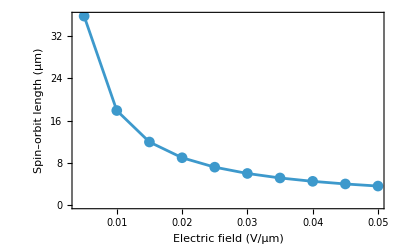

```mathematica
Ez = rashbaz[[;;,1]];
alphaz = rashbaz[[;;,2]]*100 (*meV nm*)
alphazprime = (alphaz[[-1]] - alphaz[[2]])*1000/(Ez[[-1]] -Ez[[2]]); (*meV nm2/V*)
(*ListPlot[Transpose[{Ey,alphay}]]*)
Print["α' = ", SetPrecision[alphazprime,5], " meV nm2/V"]

(* Spin–orbit length: lSO = hbar^2/(m* |alpha|) *)
Print["Calculating spin–orbit length:"];

my = 0.524; (* mass along x, in units of m0 *)
hbar2OverM0 = 76.19964; (* meV nm^2 *)

(* Start at the second data point, as in your original code *)
lsoValues = Table[
   If[
     alphaz[[i]] == 0,
     Infinity,
     hbar2OverM0/(my*Abs[alphaz[[i]]]*1000)
   ],
   {i, 2, Length[alphaz]}
];

(* Columns: electric field, spin–orbit length *)
lsoData = Transpose[{Ez[[2 ;;]], lsoValues}];

Print[
  Grid[
    Prepend[
      lsoData,
      {"Electric field (V/µm)", "Spin–orbit length (μm)"}
    ],
    Frame -> All
  ]
];

(* Exclude infinite lengths from the plot *)
finiteLsoData = Select[lsoData, Last[#] =!= Infinity &];

Print[
  ListLinePlot[
    finiteLsoData,
    Frame -> True,
    FrameLabel -> {
      "Electric field (V/µm)",
      "Spin–orbit length (μm)"
    },
    PlotMarkers -> Automatic,
    PlotRange -> All
  ]
];
```